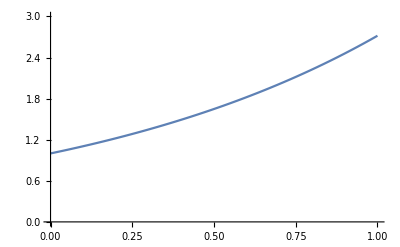

```mathematica
f[x_]:=Exp[x]
Plot[Exp[x],{x,0,1},PlotRange->{0,3},PlotLegends->"Expressions"]
```

1+x+x^2/2+O[x]^3

1+x+x^2/2

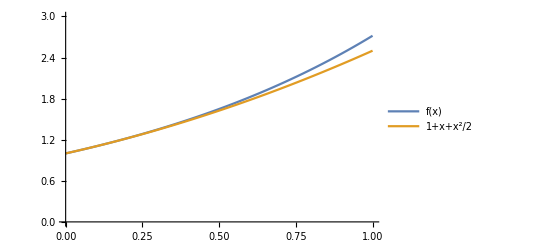

```mathematica
Series[f[x],{x,0,2}] (* Changed to second order after class for consistency. *)
Normal[Series[f[x],{x,0,2}]]
Plot[{f[x],Evaluate[Normal[Series[f[x],{x,0,2}]]]},{x,0,1},PlotRange->{0,3},PlotLegends->"Expressions"]
```

```mathematica
PadeApproximant[f[x],{x,0,{1,1}}] (* Parameterized Pade approximations. *)
PadeApproximant[f[x],{x,0,{2,0}}]
PadeApproximant[f[x],{x,0,{0,2}}]
```

(1+x/2)/(1-x/2)

1+x+x^2/2

1/(1-x+x^2/2)

```mathematica
?PadeApproximant
(* Used to verify arguments. *)
```

PadeApproximant[expr,{x,x_0,{m,n}}] gives the Padé approximant to expr about the point x=x_0, with numerator order m and denominator order n.
PadeApproximant[expr,{x,x_0,n}] gives the diagonal Padé approximant to expr about the point x=x_0 of order n.

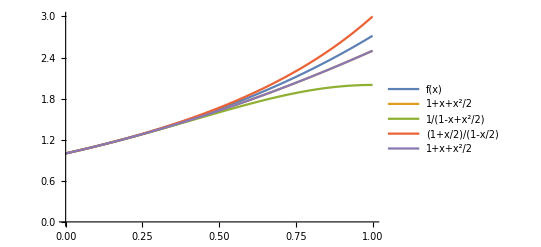

```mathematica
Series[f[x],{x,0,2}];
Normal[Series[f[x],{x,0,2}]];
Plot[{f[x],Evaluate[Normal[Series[f[x],{x,0,2}]]], Evaluate[PadeApproximant[f[x],{x,0,{0,2}}]],Evaluate[PadeApproximant[f[x],{x,0,{1,1}}]],Evaluate[PadeApproximant[f[x],{x,0,{2,0}}]]},{x,0,1},PlotRange->{0,3},PlotLegends->"Expressions"]
```

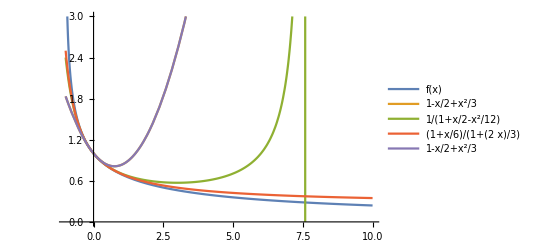

```mathematica
(* You are encouraged to adapt this code for other functions. *)
f[x_]:=Log[1+x]/x
Plot[{f[x],Evaluate[Normal[Series[f[x],{x,0,2}]]], Evaluate[PadeApproximant[f[x],{x,0,{0,2}}]],Evaluate[PadeApproximant[f[x],{x,0,{1,1}}]],Evaluate[PadeApproximant[f[x],{x,0,{2,0}}]]},{x,-1,10},PlotRange->{0,3},PlotLegends->"Expressions"]
(* Notice how amazingly well the linear/linear approximation works. A quadratic/quadratic is almost indistinguishable from the original function at this scale, while a 4th order Maclaurin series is quite a terrible approximation. *)
```